```mathematica
SetDirectory[NotebookDirectory[]]
<<OperatorGB.m
```

/Users/clemenshofstadler/Desktop/OperatorGB

Package OperatorGB version 1.1.1
Copyright 2019, Institute for Algebra, JKU
written by Clemens Hofstadler

## Werner

```mathematica
SetUpRing[{a,b,SuperMinus[a],SuperMinus[b],i}];
```

a < b < a^- < b^- < i

```mathematica
Q ={{a,2,1},{SuperMinus[a],1,2},{i,2,2},{b,3,2},{SuperMinus[b],2,3}};
```

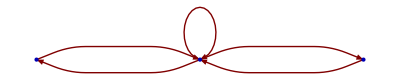

```mathematica
PlotQuiver[Q]
```

```mathematica
assumptions = {a**SuperMinus[a]**a-a,
		b**SuperMinus[b]**b-b,
		b**SuperMinus[b]**i-b**SuperMinus[b]**SuperMinus[a]**a-i+SuperMinus[a]**a,i**b-b};
claim = a**b**SuperMinus[b]**SuperMinus[a]**a**b-a**b;
```

```mathematica
QSignature[#,Q]&/@assumptions
```

{{{2,1}},{{3,2}},{{2,2}},{{3,2}}}

```mathematica
G = Groebner[cofactors,assumptions,Info->True,Parallel->False];
```

G has 4 elements in the beginning.

6 ambiguities in total (computation took 0.000701)

Removed 0 ambiguities in 0.000456

Generating S-polys: 0.000681 (4 in total)

Reducing S-polys: 0.000506 (2 remaining)

The second reduction took 0.28578

Iteration 1 finished. G has now 6 elements

5 ambiguities in total (computation took 0.000942)

Removed 0 ambiguities in 0.000458

Generating S-polys: 0.000711 (5 in total)

Reducing S-polys: 0.000613 (3 remaining)

The second reduction took 0.181598

Iteration 2 finished. G has now 8 elements

10 ambiguities in total (computation took 0.001334)

Removed 2 ambiguities in 0.00084

Generating S-polys: 0.001133 (7 in total)

Reducing S-polys: 0.000814 (0 remaining)

Rewriting the cofactors has started.

Rewriting the cofactors took in total 0.179115

```mathematica
ReducedForm[vars,G,claim]
```

0

```mathematica
( Rewrite[vars,cofactors]//MultiplyOut)===claim
```

True

```mathematica
(*only linear combination in terms of monic versions of generators*) 
Rewrite[vars,cofactors]/.Map[{_,#,_}->Nothing&,assumptions]
Rewrite[vars,cofactors]/.Map[{_,#/LeadingTerm[#][[1]],_}->Nothing&,assumptions]
```

{{a,i-a^-**a-b**b^-**i+b**b^-**a^-**a,b}}

{}

```mathematica
(*now we do all at once - and get linear combination in terms of generators and not their monic versions*)
```

```mathematica
certificate =Certify[assumptions,claim,Q,Info->True,Criterion->True];
```

Using the following monomial ordering:

a < a^- < i < b < b^-

Interreduced the input from 4 polynomials to 4.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 4 elements in the beginning.

6 ambiguities in total (computation took 0.004573)

Removed 0 ambiguities in 0.000392

Generating S-polys: 0.006725 (4 in total)

Reducing S-polys: 0.000468 (2 remaining)

The second reduction took 0.265477

Iteration 1 finished. G has now 6 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.000497

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut[certificate[[4]]]===claim
```

True

```mathematica
certificate[[4]]/.Map[{__,#,__}->Nothing&,assumptions]
```

{}

## Hartwig (small version)

```mathematica
Q = {{a,3,4},{adj[a],4,3},
{b,2,3},{adj[b],3,2},
{c,1,2},{adj[c],2,1},
{SuperDagger[a],4,3},{adj[SuperDagger[a]],3,4},
{SuperDagger[b],3,2},{adj[SuperDagger[b]],2,3},
{SuperDagger[c],2,1},{adj[SuperDagger[c]],1,2},
{m,1,4},{adj[m],4,1},
{SuperDagger[m],4,1},{adj[SuperDagger[m]],1,4}};
```

```mathematica
Clear[m];
MatP =  SuperDagger[a]**a**b**c**SuperDagger[c];
MatQ = c**SuperDagger[c]**SuperDagger[b]**SuperDagger[a]**a;
DefM = {m-a**b**c,SuperDagger[m]-SuperDagger[c]**SuperDagger[b]**SuperDagger[a]};
cond2 = {MatQ**MatP**MatQ-MatQ,MatP**MatQ**MatP-MatP,
	MatQ**MatP**c**adj[c]-adj[MatQ**MatP**c**adj[c]],
	adj[a]**a**MatP**MatQ-adj[adj[a]**a**MatP**MatQ]};
cond3 = {MatP**MatQ**MatP-MatP, MatQ**MatP**MatQ-MatQ,
	MatQ**MatP**c**adj[c]**adj[MatP]-c**adj[c]**adj[MatP],adj[MatQ]**adj[MatP]**adj[a]**a**MatP-adj[a]**a**MatP};
cond4 = {MatP**MatQ**MatP**MatQ-MatP**MatQ,
MatQ**MatP**MatQ-MatQ,MatQ**MatP**c**adj[c]**adj[MatP]-c**adj[c]**adj[MatP],
adj[MatQ]**adj[MatP]**adj[a]**a**MatP - adj[a]**a**MatP};
```

### (i) => (ii):

```mathematica
assumptions = Join[Pinv[a],Pinv[b],Pinv[c],DefM,Pinv[m]]// AddAdj;
```

```mathematica
certificate = Certify[assumptions,cond2,Q,Info->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < a^† < adj[a^†] < b^† < adj[b^†] < c^† < adj[c^†] < m < adj[m] < m^† < adj[m^†]

Interreduced the input from 36 polynomials to 28.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 28 elements in the beginning.

52 ambiguities in total (computation took 0.030064)

Removed 0 ambiguities in 0.005809

Generating S-polys: 0.031949 (44 in total)

Reducing S-polys: 0.003269 (12 remaining)

The second reduction took 0.136927

Iteration 1 finished. G has now 40 elements

Starting iteration 2...

G has 40 elements in the beginning.

48 ambiguities in total (computation took 0.053576)

Removed 0 ambiguities in 0.009382

Generating S-polys: 0.036544 (42 in total)

Reducing S-polys: 0.00536 (26 remaining)

The second reduction took 0.163179

Iteration 2 finished. G has now 56 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.008318

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond2
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

### (ii) => (i):

```mathematica
assumptions = Join[Pinv[a],Pinv[b],Pinv[c],DefM,cond2]// AddAdj;
```

```mathematica
certificate = Certify[assumptions,Pinv[m],Q,Info->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < a^† < adj[a^†] < b^† < adj[b^†] < c^† < adj[c^†] < m < adj[m] < m^† < adj[m^†]

Interreduced the input from 36 polynomials to 28.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 28 elements in the beginning.

85 ambiguities in total (computation took 0.034235)

Removed 5 ambiguities in 0.010421

Generating S-polys: 0.048768 (71 in total)

Reducing S-polys: 0.010025 (42 remaining)

The second reduction took 0.117782

Iteration 1 finished. G has now 66 elements

Starting iteration 2...

G has 66 elements in the beginning.

354 ambiguities in total (computation took 0.152508)

Removed 81 ambiguities in 0.077806

Generating S-polys: 0.131636 (263 in total)

Reducing S-polys: 0.05328 (131 remaining)

The second reduction took 0.378582

Iteration 2 finished. G has now 138 elements

Starting iteration 3...

G has 138 elements in the beginning.

1594 ambiguities in total (computation took 0.392026)

Removed 705 ambiguities in 0.586587

Generating S-polys: 0.363226 (795 in total)

Reducing S-polys: 0.215869 (166 remaining)

The second reduction took 0.183898

Iteration 3 finished. G has now 188 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.038168

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===Pinv[m]
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

### (ii) => (iii):

```mathematica
assumptions = Join[Pinv[a],Pinv[b],Pinv[c],cond2]// AddAdj;
certificate = Certify[assumptions,cond3,Q,Info->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < a^† < adj[a^†] < b^† < adj[b^†] < c^† < adj[c^†] < m < adj[m] < m^† < adj[m^†]

Interreduced the input from 32 polynomials to 24.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 24 elements in the beginning.

78 ambiguities in total (computation took 0.032033)

Removed 10 ambiguities in 0.011414

Generating S-polys: 0.05099 (56 in total)

Reducing S-polys: 0.008775 (24 remaining)

The second reduction took 0.193589

Iteration 1 finished. G has now 47 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.004899

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond3
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

### (iii) => (ii):

```mathematica
assumptions = Join[Pinv[a],Pinv[b],Pinv[c],cond3]// AddAdj;
certificate = Certify[assumptions,cond2,Q,Info->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < a^† < adj[a^†] < b^† < adj[b^†] < c^† < adj[c^†] < m < adj[m] < m^† < adj[m^†]

Interreduced the input from 32 polynomials to 26.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 26 elements in the beginning.

110 ambiguities in total (computation took 0.033031)

Removed 13 ambiguities in 0.017416

Generating S-polys: 0.068862 (78 in total)

Reducing S-polys: 0.013316 (42 remaining)

The second reduction took 0.140141

Iteration 1 finished. G has now 63 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.00574

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond2
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

### (ii) => (iv):

```mathematica
assumptions = Join[Pinv[a],Pinv[b],Pinv[c],cond2]// AddAdj;
certificate = Certify[assumptions,cond4,Q,Info->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < a^† < adj[a^†] < b^† < adj[b^†] < c^† < adj[c^†] < m < adj[m] < m^† < adj[m^†]

Interreduced the input from 32 polynomials to 24.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 24 elements in the beginning.

78 ambiguities in total (computation took 0.028035)

Removed 10 ambiguities in 0.009728

Generating S-polys: 0.047842 (56 in total)

Reducing S-polys: 0.008556 (24 remaining)

The second reduction took 0.204051

Iteration 1 finished. G has now 47 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.006356

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond4
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

### (iv) => (ii):

```mathematica
assumptions = Join[Pinv[a],Pinv[b],Pinv[c],cond4]// AddAdj;
certificate = Certify[assumptions,cond2,Q,Info->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < a^† < adj[a^†] < b^† < adj[b^†] < c^† < adj[c^†] < m < adj[m] < m^† < adj[m^†]

Interreduced the input from 32 polynomials to 24.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 24 elements in the beginning.

82 ambiguities in total (computation took 0.027662)

Removed 4 ambiguities in 0.011638

Generating S-polys: 0.057957 (64 in total)

Reducing S-polys: 0.011827 (34 remaining)

The second reduction took 0.142391

Iteration 1 finished. G has now 53 elements

Starting iteration 2...

G has 53 elements in the beginning.

701 ambiguities in total (computation took 0.161112)

Removed 408 ambiguities in 0.146418

Generating S-polys: 0.214031 (231 in total)

Reducing S-polys: 0.06006 (121 remaining)

The second reduction took 0.263462

Iteration 2 finished. G has now 95 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.008863

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond2
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

### (iii) => (iv):

```mathematica
assumptions = Join[Pinv[a],Pinv[b],Pinv[c],cond3]// AddAdj;
certificate = Certify[assumptions,cond4,Q,Info->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < a^† < adj[a^†] < b^† < adj[b^†] < c^† < adj[c^†] < m < adj[m] < m^† < adj[m^†]

Interreduced the input from 32 polynomials to 26.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 26 elements in the beginning.

110 ambiguities in total (computation took 0.034728)

Removed 13 ambiguities in 0.017164

Generating S-polys: 0.069973 (78 in total)

Reducing S-polys: 0.015347 (42 remaining)

The second reduction took 0.174263

Iteration 1 finished. G has now 63 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.004363

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond4
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

### (iv) => (iii):

```mathematica
assumptions = Join[Pinv[a],Pinv[b],Pinv[c],cond4]// AddAdj;
certificate = Certify[assumptions,cond3,Q,Info->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < a^† < adj[a^†] < b^† < adj[b^†] < c^† < adj[c^†] < m < adj[m] < m^† < adj[m^†]

Interreduced the input from 32 polynomials to 24.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 24 elements in the beginning.

82 ambiguities in total (computation took 0.029255)

Removed 4 ambiguities in 0.012458

Generating S-polys: 0.04724 (64 in total)

Reducing S-polys: 0.010247 (34 remaining)

The second reduction took 0.165499

Iteration 1 finished. G has now 53 elements

Starting iteration 2...

G has 53 elements in the beginning.

701 ambiguities in total (computation took 0.184006)

Removed 408 ambiguities in 0.155112

Generating S-polys: 0.213473 (231 in total)

Reducing S-polys: 0.055492 (121 remaining)

The second reduction took 0.194805

Iteration 2 finished. G has now 95 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.009262

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond3
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

### (i) => (iii):

```mathematica
assumptions = Join[Pinv[a],Pinv[b],Pinv[c],DefM,Pinv[m]]// AddAdj;
certificate = Certify[assumptions,cond3,Q,Info->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < a^† < adj[a^†] < b^† < adj[b^†] < c^† < adj[c^†] < m < adj[m] < m^† < adj[m^†]

Interreduced the input from 36 polynomials to 28.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 28 elements in the beginning.

52 ambiguities in total (computation took 0.027328)

Removed 0 ambiguities in 0.005884

Generating S-polys: 0.032916 (44 in total)

Reducing S-polys: 0.00375 (12 remaining)

The second reduction took 0.189309

Iteration 1 finished. G has now 40 elements

Starting iteration 2...

G has 40 elements in the beginning.

48 ambiguities in total (computation took 0.053776)

Removed 0 ambiguities in 0.007815

Generating S-polys: 0.035656 (42 in total)

Reducing S-polys: 0.006089 (26 remaining)

The second reduction took 0.216723

Iteration 2 finished. G has now 56 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.005194

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond3
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

### (i) => (iv):

```mathematica
assumptions = Join[Pinv[a],Pinv[b],Pinv[c],DefM,Pinv[m]]// AddAdj;
certificate = Certify[assumptions,cond4,Q,Info->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < a^† < adj[a^†] < b^† < adj[b^†] < c^† < adj[c^†] < m < adj[m] < m^† < adj[m^†]

Interreduced the input from 36 polynomials to 28.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 28 elements in the beginning.

52 ambiguities in total (computation took 0.027504)

Removed 0 ambiguities in 0.005793

Generating S-polys: 0.031109 (44 in total)

Reducing S-polys: 0.003276 (12 remaining)

The second reduction took 0.14349

Iteration 1 finished. G has now 40 elements

Starting iteration 2...

G has 40 elements in the beginning.

48 ambiguities in total (computation took 0.055633)

Removed 0 ambiguities in 0.007689

Generating S-polys: 0.035963 (42 in total)

Reducing S-polys: 0.005933 (26 remaining)

The second reduction took 0.103977

Iteration 2 finished. G has now 56 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.005979

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===cond4
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

### (iv) => (i):

```mathematica
assumptions = Join[Pinv[a],Pinv[b],Pinv[c],DefM,cond4]// AddAdj;
certificate = Certify[assumptions,Pinv[m],Q,Info->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < a^† < adj[a^†] < b^† < adj[b^†] < c^† < adj[c^†] < m < adj[m] < m^† < adj[m^†]

Interreduced the input from 36 polynomials to 29.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 29 elements in the beginning.

87 ambiguities in total (computation took 0.037766)

Removed 0 ambiguities in 0.011471

Generating S-polys: 0.042351 (77 in total)

Reducing S-polys: 0.010092 (47 remaining)

The second reduction took 0.149315

Iteration 1 finished. G has now 69 elements

Starting iteration 2...

G has 69 elements in the beginning.

407 ambiguities in total (computation took 0.159962)

Removed 90 ambiguities in 0.09474

Generating S-polys: 0.150142 (294 in total)

Reducing S-polys: 0.060677 (126 remaining)

The second reduction took 0.220394

Iteration 2 finished. G has now 128 elements

Starting iteration 3...

G has 128 elements in the beginning.

1315 ambiguities in total (computation took 0.355247)

Removed 633 ambiguities in 0.433303

Generating S-polys: 0.270507 (611 in total)

Reducing S-polys: 0.133991 (58 remaining)

The second reduction took 0.184925

Iteration 3 finished. G has now 162 elements

Starting iteration 4...

G has 162 elements in the beginning.

1242 ambiguities in total (computation took 0.26144)

Removed 826 ambiguities in 0.436552

Generating S-polys: 0.200426 (351 in total)

Reducing S-polys: 0.101657 (16 remaining)

The second reduction took 0.081732

Iteration 4 finished. G has now 169 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.018697

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===Pinv[m]
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

### (iii) => (i):

```mathematica
assumptions = Join[Pinv[a],Pinv[b],Pinv[c],DefM,cond3]// AddAdj;
certificate = Certify[assumptions,Pinv[m],Q,Info->True];
```

Using the following monomial ordering:

a < adj[a] < b < adj[b] < c < adj[c] < a^† < adj[a^†] < b^† < adj[b^†] < c^† < adj[c^†] < m < adj[m] < m^† < adj[m^†]

Interreduced the input from 36 polynomials to 30.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 30 elements in the beginning.

98 ambiguities in total (computation took 0.040645)

Removed 3 ambiguities in 0.01433

Generating S-polys: 0.058592 (83 in total)

Reducing S-polys: 0.013744 (53 remaining)

The second reduction took 0.132908

Iteration 1 finished. G has now 75 elements

Starting iteration 2...

G has 75 elements in the beginning.

481 ambiguities in total (computation took 0.183526)

Removed 112 ambiguities in 0.116659

Generating S-polys: 0.17517 (341 in total)

Reducing S-polys: 0.0724 (133 remaining)

The second reduction took 0.213722

Iteration 2 finished. G has now 143 elements

Starting iteration 3...

G has 143 elements in the beginning.

1703 ambiguities in total (computation took 0.401303)

Removed 948 ambiguities in 0.553881

Generating S-polys: 0.293661 (652 in total)

Reducing S-polys: 0.150665 (50 remaining)

The second reduction took 0.112843

Iteration 3 finished. G has now 175 elements

Starting iteration 4...

G has 175 elements in the beginning.

1248 ambiguities in total (computation took 0.283139)

Removed 845 ambiguities in 0.462457

Generating S-polys: 0.186823 (342 in total)

Reducing S-polys: 0.104076 (16 remaining)

The second reduction took 0.094539

Iteration 4 finished. G has now 182 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.020802

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===Pinv[m]
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{},{},{}}

## General inverses

```mathematica
Clear[p,q,g,a,b];
Q= {{p,1,1},{q,1,1},{a,1,2},{g[a],2,1},{b,2,1},{g[b],1,2}};
```

```mathematica
ginvA = {-a+a**g[a]**a,-g[a]+g[a]**a**g[a]};
ginvB = {-b+b**g[b]**b,-g[b]+g[b]**b**g[b]};
ROL = {-a**b+a**b**g[b]**g[a]**a**b,-g[b]**g[a]+g[b]**g[a]**a**b**g[b]**g[a]};
proj = {p-g[a]**a,q-b**g[b]};
additionalCondition = {p**q-q**p};
assumptions = Join[ginvA,ginvB,proj,additionalCondition];
```

```mathematica
certificate = Certify[assumptions,ROL,Q,Info->True];
```

Using the following monomial ordering:

p < q < a < g[a] < b < g[b]

Interreduced the input from 7 polynomials to 7.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 7 elements in the beginning.

8 ambiguities in total (computation took 0.003855)

Removed 0 ambiguities in 0.000471

Generating S-polys: 0.017232 (6 in total)

Reducing S-polys: 0.000366 (6 remaining)

The second reduction took 0.185903

Iteration 1 finished. G has now 11 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.000744

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut/@certificate[[4]]===ROL
certificate[[4]]//.Map[{_,#,_}->Nothing&,assumptions]
```

True

{{},{}}

## Inner Inverses

```mathematica
Q= {{a,1,2},{aa,2,1},{b,2,1},{bb,1,2},{i,1,1}};
```

```mathematica
innerinv = {-a+a**aa**a,-b+b**bb**b};
cond = {-i+aa**a+b**bb**i-b**bb**aa**a};
prop = {-i+i**i,a**i-a,-aa+i**aa,-b+i**b,-bb+bb**i};
claim =-a**b+a**b**bb**aa**a**b;
```

```mathematica
assumptions = Join[innerinv,cond,prop];
```

```mathematica
certificate = Certify[assumptions,claim,Q,Info->True];
```

Using the following monomial ordering:

a < aa < b < bb < i

Interreduced the input from 8 polynomials to 8.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 8 elements in the beginning.

17 ambiguities in total (computation took 0.006385)

Removed 0 ambiguities in 0.001253

Generating S-polys: 0.007778 (6 in total)

Reducing S-polys: 0.000561 (0 remaining)

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.000366

Done! All claims were successfully reduced to 0.

```mathematica
MultiplyOut[certificate[[4]]]===claim
certificate[[4]]/.Map[{_,#,_}->Nothing&,assumptions]
```

True

{}

## Moore-Penrose inverse is unique

```mathematica
Q = {{a,A,B},{adj[a],B,A},{SuperDagger[a1],B,A},{adj[SuperDagger[a1]],A,B},{SuperDagger[a2],B,A},{adj[SuperDagger[a2]],A,B}};
assumptions= Join[Pinv[a,SuperDagger[a1]],Pinv[a,SuperDagger[a2]]]//AddAdj;
```

```mathematica
certificate  = Certify[assumptions,SuperDagger[a1]-SuperDagger[a2],Q,Info->True];
```

Using the following monomial ordering:

a < adj[a] < a1^† < adj[a1^†] < a2^† < adj[a2^†]

Interreduced the input from 16 polynomials to 12.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 12 elements in the beginning.

28 ambiguities in total (computation took 0.008772)

Removed 0 ambiguities in 0.00199

Generating S-polys: 0.023179 (24 in total)

Reducing S-polys: 0.001705 (8 remaining)

The second reduction took 0.157254

Iteration 1 finished. G has now 18 elements

Starting iteration 2...

G has 18 elements in the beginning.

28 ambiguities in total (computation took 0.015529)

Removed 2 ambiguities in 0.002831

Generating S-polys: 0.014107 (24 in total)

Reducing S-polys: 0.002588 (9 remaining)

The second reduction took 0.147876

Iteration 2 finished. G has now 23 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.001303

Done! All claims were successfully reduced to 0.

```mathematica
certificate[[4]]//MultiplyOut
certificate[[4]]/.Map[{_,#,_}->Nothing&,assumptions]
```

a1^†-a2^†

{}

## Moore-Penrose inverse and singular value decomposition (does not work)

```mathematica
A = {u**Σ**vInv};
U = {u**uInv - iu, uInv**u-iu,iu**iu-iu,adj[u]-uInv};
V = {v**vInv - iv, vInv**v-iv,iv**iv-iv,adj[v]-vInv};
assumptions = Join[A,Pinv[a],U,V,Pinv[Σ]]//AddAdj;
claim = SuperDagger[a]-v**SuperDagger[Σ]**uInv;
```

```mathematica
Q = TrivialQuiver[Join[assumptions,{claim}]];
```

```mathematica
certificate = Certify[assumptions,claim,Q,Info->True];
```

Using the following monomial ordering:

u < Σ < vInv < a < a^† < adj[a^†] < adj[a] < iu < uInv < adj[u] < iv < v < adj[v] < Σ^† < adj[Σ^†] < adj[Σ] < adj[vInv] < adj[iu] < adj[uInv] < adj[iv]

Interreduced the input from 34 polynomials to 26.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 26 elements in the beginning.

36 ambiguities in total (computation took 0.023987)

Removed 6 ambiguities in 0.003173

Generating S-polys: 0.024456 (16 in total)

Reducing S-polys: 0.001779 (12 remaining)

The second reduction took 0.188631

Iteration 1 finished. G has now 38 elements

Starting iteration 2...

G has 38 elements in the beginning.

50 ambiguities in total (computation took 0.046942)

Removed 8 ambiguities in 0.005735

Generating S-polys: 0.027958 (34 in total)

Reducing S-polys: 0.00207 (12 remaining)

The second reduction took 0.167183

Iteration 2 finished. G has now 44 elements

Starting iteration 3...

G has 44 elements in the beginning.

41 ambiguities in total (computation took 0.044745)

Removed 1 ambiguities in 0.006667

Generating S-polys: 0.026828 (30 in total)

Reducing S-polys: 0.002156 (6 remaining)

The second reduction took 0.395644

Iteration 3 finished. G has now 48 elements

Starting iteration 4...

G has 48 elements in the beginning.

41 ambiguities in total (computation took 0.022435)

Removed 8 ambiguities in 0.006579

Generating S-polys: 0.027966 (20 in total)

Reducing S-polys: 0.00139 (6 remaining)

The second reduction took 0.163852

Iteration 4 finished. G has now 52 elements

Starting iteration 5...

G has 52 elements in the beginning.

51 ambiguities in total (computation took 0.046504)

Removed 16 ambiguities in 0.008369

Generating S-polys: 0.028302 (20 in total)

Reducing S-polys: 0.001411 (6 remaining)

The second reduction took 0.33689

Iteration 5 finished. G has now 56 elements

Starting iteration 6...

G has 56 elements in the beginning.

61 ambiguities in total (computation took 0.038658)

Removed 24 ambiguities in 0.009655

Generating S-polys: 0.020438 (20 in total)

Reducing S-polys: 0.001683 (6 remaining)

The second reduction took 0.109324

Iteration 6 finished. G has now 60 elements

Starting iteration 7...

G has 60 elements in the beginning.

71 ambiguities in total (computation took 0.038643)

Removed 32 ambiguities in 0.011735

Generating S-polys: 0.033438 (20 in total)

Reducing S-polys: 0.001688 (6 remaining)

The second reduction took 0.114553

Iteration 7 finished. G has now 64 elements

Starting iteration 8...

G has 64 elements in the beginning.

81 ambiguities in total (computation took 0.051647)

Removed 40 ambiguities in 0.013242

Generating S-polys: 0.034781 (20 in total)

Reducing S-polys: 0.001945 (6 remaining)

The second reduction took 0.133217

Iteration 8 finished. G has now 68 elements

Starting iteration 9...

G has 68 elements in the beginning.

91 ambiguities in total (computation took 0.04032)

Removed 48 ambiguities in 0.015042

Generating S-polys: 0.036054 (20 in total)

Reducing S-polys: 0.001949 (6 remaining)

The second reduction took 0.144487

Iteration 9 finished. G has now 72 elements

Starting iteration 10...

G has 72 elements in the beginning.

101 ambiguities in total (computation took 0.057434)

Removed 56 ambiguities in 0.020685

Generating S-polys: 0.045427 (20 in total)

Reducing S-polys: 0.002419 (6 remaining)

The second reduction took 0.191263

Iteration 10 finished. G has now 76 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.000334

Done! Not all claims could be reduced to 0.

```mathematica
certificate[[3]]
```

-v**Σ^†**uInv+a^†

## Cancallation lemma (A^*A = 0 => A = 0 if A has Moore-Penrose inverse)

```mathematica
assumptions = Join[Pinv[a],{adj[a]**a}]//AddAdj;
```

```mathematica
Q = {{a,X,Y},{adj[a],Y,X},{SuperDagger[a],Y,X},{adj[SuperDagger[a]],X,Y}};
```

```mathematica
certificate  = Certify[assumptions,a,Q,Info->True];
```

Using the following monomial ordering:

a < adj[a] < a^† < adj[a^†]

Interreduced the input from 10 polynomials to 4.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 4 elements in the beginning.

0 ambiguities in total (computation took 0.003883)

Removed 0 ambiguities in 2.×10^-6

Generating S-polys: 0.002373 (0 in total)

Reducing S-polys: 0.00002 (0 remaining)

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.000092

Done! All claims were successfully reduced to 0.

```mathematica
certificate[[3]]
```

0

## Woodbury matrix inversion identity

```mathematica
A = a+u**c**v;
InvA = inva-inva**u**invs**v**inva;
s = invc+ v**inva**u;
```

```mathematica
InverseA = {a**inva - ia, inva**a-ia};
InverseC = {c**invc - ic, invc**c-ic};
InverseS = {s**invs-ic,invs**s-ic};
Id = {a**ia-a,ia**a-a,ia**ia-ia,c**ic-c,ic**c-c,ic**ic-ic,A**ia -A,ia**A-A,inva**ia-inva,ia**inva-inva,invc**ic-invc,ic**invc-invc,InvA**ia-InvA,ia**InvA-InvA,s**ic-s,ic**s-ic,invs**ic-invs,ic**invs-invs};

assumptions = Distribute/@Join[InverseA,InverseC,InverseS,Id];
claims = Distribute/@{A**InvA-ia,InvA**A-ia};
```

```mathematica
Q = {{a,1,1},{inva,1,1},{u,2,1},{v,1,2},{c,2,2},{invc,2,2},{invs,2,2},{ia,1,1},{ic,2,2}};
```

```mathematica
certificate =  Certify[assumptions,claims,Q,Info->True];
```

Using the following monomial ordering:

a < inva < u < v < c < invc < invs < ia < ic

Interreduced the input from 24 polynomials to 22.

Computing a (partial) Groebner basis and reducing the claim...

Starting iteration 1...

G has 22 elements in the beginning.

70 ambiguities in total (computation took 0.016503)

Removed 0 ambiguities in 0.005871

Generating S-polys: 0.027476 (34 in total)

Reducing S-polys: 0.002411 (9 remaining)

The second reduction took 0.189206

Iteration 1 finished. G has now 26 elements

Rewriting the cofactors has started...

Rewriting the cofactors took in total 0.001967

Done! All claims were successfully reduced to 0.

```mathematica
(*our results are always expanded but NonCommutativeMultiply can not expand terms automatically 
*)
MultiplyOut/@certificate[[4]]===ToNonCommutativeMultiply/@ToProd/@claims
```

True

```mathematica
certificate[[4]]/.Map[{_,ToNonCommutativeMultiply[ToProd[#]],_}->Nothing&,assumptions]
```

{{},{}}